# MA255 Tech Lab Assignment #2

## I. Partial Derivatives

#### a. Use the definition of the derivative to find the partial derivatives of F with respect to x and with respect to y

```mathematica
f[x_,y_]=ⅇ^(-1/12 x^3 + x- y^2 + 2 y);
a=3;
b=1;
Limit[(f[a+h,b]-f[a,b])/h,h->0]
Limit[(f[a,b+h]-f[a,b])/h,h->0]
```

-(5 ⅇ^(7/4))/4

0

Evaluating the partial derivative with respect to x, we obtain -(5 ⅇ^(7/4))/4 as the limit. 
Evaluating the partial derivative with respect to y, we obtain 0 as the limit.

#### b. Plot the function in R^3 on the domain

```mathematica
Plot3D[f[x,y],{x,1,4},{y,-5,5},PlotRange->{0,12}]
```

-Graphics3D-

#### c. Plot the function and the curves, including tangent lines

```mathematica
γ[t_]={t,1,f[t,1]};
α[s_]={3,s,f[3,s]};
g1=Plot3D[f[x,y],{x,1,4},{y,-5,5},PlotRange->{0,12}];
g2=ParametricPlot3D[γ[t],{t,1,4},PlotRange->{0,12},PlotStyle->Red];
g3=ParametricPlot3D[α[s],{s,-5,5},PlotRange->{0,12},PlotStyle->Blue];
g4=ParametricPlot3D[{3+t,1,5.755-7.18325*t},{t,-10,10},PlotRange->{0,12},PlotStyle->Green];
g5=ParametricPlot3D[{3,1+t,5.746},{t,-5,5},PlotRange->{0,12},PlotStyle->Black];
Show[{g1,g2,g3,g4,g5},Axes->True,AxesLabel->{"x","y","z"}]
```

-Graphics3D-

This graph shows the original 3D Plot of the original function, exploring the curves of the function and the tangent lines. You can determine which segment is which by the color, which is designated in the code.
The tangent lines to the curve represent how the function is changing at the certain point on the original function with respect to x (green) and y (black).

#### d. Create a 2D Plot of u(x)=f(3,x) and v(y)=f(y,1)

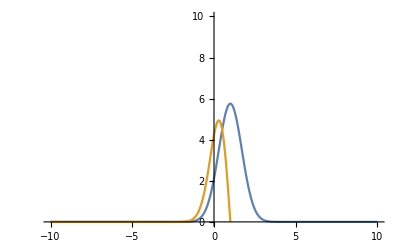

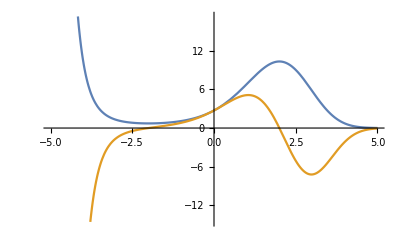

```mathematica
u[x_]=f[3,x];
v[y_]=f[y,1];
p1=Plot[{u[x],u'[x]},{x,-10,10},PlotRange->{0,10}]
p2=Plot[{v[y],v'[y]},{y,-5,5}]
```

These are the 2D graphs of the functions and their tangent lines. Blue is the original function and gold represents their tangent lines. These are the 2D traces of the α and γ functions respectively from the 3D representation of the function.

## II. Tangent Planes

Now, we’ll move on to visualizing tangent planes, given functions in 3D, as it can sometimes be difficult to visualize without knowing what is going on.

#### a. Plot the given function, g(x,y)= 25 - 4 x^3-y^5 in R^3 on the specified domain

```mathematica
g[x_,y_]=25-4 x^3-y^5;
Plot3D[g[x,y],{x,0,2},{y,0,2},Axes->True,AxesLabel->{"x","y","z"}]
```

-Graphics3D-

#### b. Find the equation of the tangent plane that passes through (2,2)

We can use the equation z-z_0=f_x(x-x_0)+f_y(y-y_0) to find the equation of the tangent plane.

```mathematica
Subscript[x, 0]=2;
Subscript[y, 0]=2;
Subscript[f, x]=D[g[x,y],x];
Subscript[f, y]=D[g[x,y],y];
Subscript[f, x] (x-Subscript[x, 0])+Subscript[f, y] (y-Subscript[y, 0])
```

-12 (-2+x) x^2-5 (-2+y) y^4

Therefore, the equation of our tangent plane is z= -12 x^3-5 y^5+34

#### c. Graphically show the function g(x,y) and the tangent plane.

```mathematica
tp=Plot3D[-12 (-2+x) x^2-5 (-2+y) y^4,{x,0,5},{y,0,5},PlotStyle->Blue];
gp=Plot3D[g[x,y],{x,0,5},{y,0,5},Axes->True,AxesLabel->{"x","y","z"}];
Show[{tp,gp},Axes->True,AxesLabel->{"x","y","z"}]
```

-Graphics3D-

This graph shows the original function and the tangent plane at g(2,2). The tangent plane is blue while the original function is orange. The point of intersection of the original function and the tangent plane is marked by
the blue area on the orange function. This area is the intersection at g(2,2).

## III. Gradient Fields

Now, we will visualize gradient fields which have applications in analyzing change in a specific direction. We can apply this to flow of matter and often, flood damage. Given an equation, we can make a “relief map” by graphing a vector field.

#### Given the Function, w(x,y)=36-2x-1/3 x^3+xy+2y-1/3 y^3:

#### a. Plot a relief map for the given region. Then plot a vector field on the map depicting the direction of water flow.

-Graphics3D-

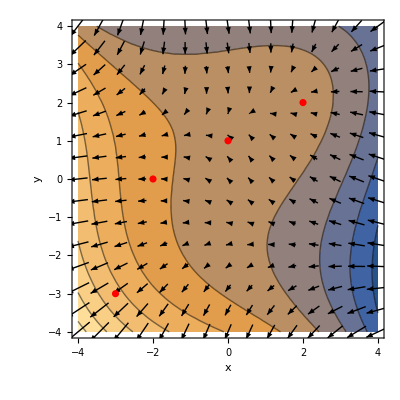

```mathematica
c=ContourPlot[w[x,y],{x,-4,4},{y,-4,4}];
Plot3D[w[x,y],{x,-4,4},{y,-4,4},Axes->True,AxesLabel->{"x","y"}]
w[x_,y_]=36-2*x-1/3*x^3+x*y+2*y-y^3/3;
wx=D[w[x,y],x];
wy=D[w[x,y],y];
v=VectorPlot[{wx,wy},{x,-4,4},{y,-4,4},VectorStyle->{Black,Large,Arrow->Large}];
Show[{c,v,ListPlot[{{0,1},{-2,0},{-3,-3},{2,2}},PlotStyle->{Red,Larger}]},Axes->True,AxesLabel->{"x","y"}]
```

This graph is an overlay of a relief map and a vector field. The vector field shows the rate at which the ground water surges and in which direction. The red dots denote the cities that are mentioned in part 3b.

#### b. Estimate which of the towns will observe the slowest and fastest groundwater surge and then calculate the groundwater speed to verify your claim.

Using the contour plot and the vector field, I estimate that the town that will receive the fastest groundwater surge is town C (-3,-3) and the town that will receive the slowest groundwater surge is town A (0,1).

```mathematica
grad[x_,y_]={wx,wy}
```

{-2-x^2+y,2+x-y^2}

```mathematica
grad[-3,-3]
```

{-14,-10}

```mathematica
grad[0,1]
```

{-1,1}

We can find the groundwater surge speed by using the gradients of each point. Doing this, the gradient vector at town C is {-14,10} and the gradient vector at town A is {-1,1}.

#### c. Find the rate of change of w at Town C in the direction of Town D.

We can accomplish this by finding the directional derivative of w in the direction of town D. We can find the direction by finding the unit vector from C to D and then doing the dotproduct of this unit vector and the function w.
We find that the vector is (5,5) in the direction of Town D.

```mathematica
Dot[{-14,-10},{5/Sqrt[50],5/Sqrt[50]}]
```

-12 √2

We find that the rate of change of W at Town C in the direction of town D is -12 √2.

## IV. Constrained and Unconstrained Optimization

#### a. Find all of the critical points of h, where h (x, y) = x^3 + y^3 - 4 x^2-4 y^2-16x

To solve for the critical points of h, we have to find the partial derivatives of h with respect to x and y and solve for where they are equal to 0.

```mathematica
h[x_,y_]=x^3+y^3-4*x^2-4*y^2-16x;
hx=D[h[x,y],x];
hy=D[h[x,y],y];
Solve[hx==0,{x,y}]
Solve[hy==0,{x,y}]
```

{{x→-4/3},{x→4}}

{{y→0},{y→8/3}}

Therefore, we get that the critical values for the function are (-4/3,0), (4,8/3), (4,0), and (-4/3,8/3).

#### b. Classify all of the critical values are maxima, minima, or saddle points.

In order to classify all of the critical values, we have to do the second derivative test. We can do this by multiplying the second derivative with respect to x by the second derivative with respect to y,
subtracted by f_xy squared. However, our f_xy ends up being 0.

```mathematica
hxx=D[hx,x]
hyy=D[hy,y];
sdt=hxx*hyy//Expand
```

-8+6 x

64-48 x-48 y+36 x y

By evaluating our critical points, we get that  (-4/3,0) is a local max, (4,8/3) is a local min, (4,0) is a saddle point, and (-4/3,8/3) is a saddle point.

#### c. Produce a plot of the contours as well as its gradient.

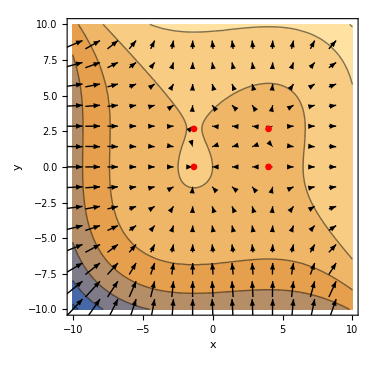

```mathematica
c=ContourPlot[h[x,y],{x,-10,10},{y,-10,10}];
v=VectorPlot[{hx,hy},{x,-10,10},{y,-10,10},VectorStyle->{Black,Large,Arrow->Large}];
Show[c,v,ListPlot[{{-4/3,0},{4,8/3},{4,0},{-4/3,8/3}},PlotStyle->{Red,Larger}],Axes->True,AxesLabel->{"x","y"}]
```

This graph is a contour and vector representation of our function h(x,y). A noticeable relationship between the countours and the gradients is the direction of the gradients flow towards the lightest areas, indicating that darker areas are
places of greater elevation and lighter areas are places with lower elevation. The gradients around the critical points (the red dots) seem to disappear greatly. For example, around the maximum point, the gradients disappear because, using the water flow example from parts c, all of the water has flowed into the maximum region and the volume of water has made this point the maximum on the contour plot. The saddle points seem to be devoid of water because there is little gradient flow into the saddle point and equally little gradient flow away from the saddle point.

## d. Produce a figure that displays the contour plot of h(x,y) and its constraint on one plot.

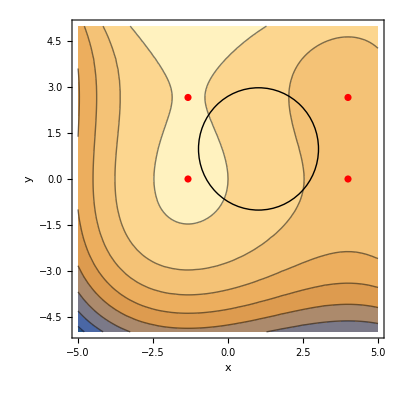

```mathematica
c=ContourPlot[h[x,y],{x,-5,5},{y,-5,5}];
con=Graphics[Circle[{1,1},2]];
Show[c,con,ListPlot[{{-4/3,0},{4,8/3},{4,0},{-4/3,8/3}},PlotStyle->{Red,Larger}],Axes->True,AxesLabel->{"x","y"}]
```

#### e. Estimate the absolute maximum and minimum values of h(x,y) subject to the constraint.

```mathematica
Maximize[{x^3+y^3-4*x^2-4*y^2-16x,(x-1)^2+(y-1)^2≤4},{x,y}]//N
Minimize[{x^3+y^3-4*x^2-4*y^2-16x,(x-1)^2+(y-1)^2≤4},{x,y}]//N
```

{9.9306,{x→-0.885212,y→0.332187}}

{-61.9306,{x→2.88521,y→1.66781}}

The absolute maximum is (-0.885,0.332) and the absolute minimum is (2.885,1.668) with values of 9.93 and -61.93 respectively.

## V. Conclusion

This tech lab allowed us to explore the visuals of partial derivatives, tangent planes, gradient fields, and unconstrained and constrained graphs.
Being able to conceptually understand the actual math behind the numbers is important to establishing the conceptual foundation for this block, especially as we start applying partial derivatives to different situations such as the Cobb Douglas Production Model.